Piecewise[{{0., x≥1||x<0}, {0.999997+1.00003 x+0.499861 x^2+0.000378232 x^3+0.0410301 x^4+0.000678505 x^5+0.000943251 x^6+0.000163344 x^7, 1/2≤x<1}, {1.+1. x+0.5 x^2+7.85784×10^-7 x^3+0.0416616 x^4+0.0000190343 x^5+0.0013468 x^6+0.000050179 x^7, True}}]

Piecewise[{{0., x≥1||x<0}, {-0.999997+0.999971 x-0.499861 x^2-0.000378168 x^3-0.0410302 x^4-0.000678435 x^5-0.000943282 x^6-0.000163338 x^7, 1/2≤x<1}, {-1.+1. x-0.5 x^2-7.85751×10^-7 x^3-0.0416616 x^4-0.0000190339 x^5-0.00134681 x^6-0.0000501787 x^7, True}}]

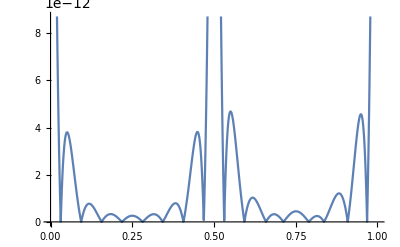

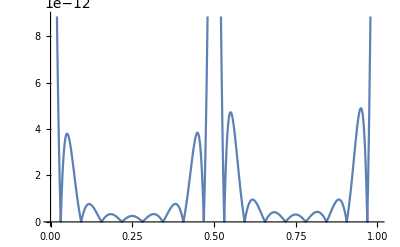

(1. | -1.
1.105 | -0.905
1.22007 | -0.82007
1.34534 | -0.74534
1.48107 | -0.68107
1.62763 | -0.62763
1.78547 | -0.58547
1.95517 | -0.55517
2.13743 | -0.53743
2.33309 | -0.53309)

(-4.6918×10^-11
-3.65485×10^-13
2.40918×10^-13
2.36478×10^-13
-3.85914×10^-13
-5.82852×10^-11
-5.16032×10^-13
2.05169×10^-13
1.45661×10^-13
-7.11875×10^-13)

(4.69141×10^-11
3.6493×10^-13
-2.43583×10^-13
-2.43916×10^-13
3.67151×10^-13
5.82034×10^-11
4.55858×10^-13
-3.04756×10^-13
-3.16525×10^-13
4.4531×10^-13)

```mathematica
Remove["Global`*"];
ψ[ii_,jj_,x_]:=Module[{},
nh=2ii-1;
Return[Piecewise[{{√(jj+1/2)2^(k/2)LegendreP[jj,2^k x-nh],(nh-1)/2^k≤ x<(nh+1)/2^k}}]];
];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,1,2^(k-1)},{j,0,M-1}]];
DD[P_]:=Module[{},
If[P==0,Return[IdentityMatrix[M*2^(k-1)]]];
H=Table[0,{i,M},{j,M}];
For[r=2,r≤ M,r++,
For[s=1,s≤ r-1,s++,
If[Mod[r+s,2]≠0,
H⟦r,s⟧=2^k √((2r-1)(2s-1));
];
];
];
Return[ArrayFlatten[Table[If[i==j,MatrixPower[H,P],0],{i,1,2^(k-1)},{j,1,2^(k-1)}]]];
];
Q[P_]:=Module[{},
X=W=Table[0,{i,1,M},{j,1,M}];
W ⟦1,1⟧=2;
X⟦1,1⟧=1;X⟦M,M⟧=1;
For[i=1,i< M,i++,
X⟦i,i+1⟧=1/(√(2i-1))1/(√(2i+1));
X⟦i+1,i⟧=-1/(√(2i-1))1/(√(2i+1));
];
Return[MatrixPower[1/2^k ArrayFlatten[Table[If[i==j,X,If[i<j,W,0]],{i,1,2^(k-1)},{j,1,2^(k-1)}]],P]];
];
β[Ι_,S_]:=Module[{ii=Ι,ss=S},
Return[A⟦ii⟧.DD[ss].Ψ[0]];
];

(***************************)
M=8;k=2;
l=2;p=2;
y0={{1,1},{-1,1}};
yreal[t_]={t+Cosh[t],t-Cosh[t]};
AA=1/π∫_0^1 yreal[x]⟦1⟧Ψ[x]ⅆx ;
BB= ∫_0^1 yreal[x]⟦2⟧Ψ[x]ⅆx ;
x0=Join[AA,BB];
(***************************)
 CC=Flatten[Table[Subscript[c, i,j],{i,1,2^(k-1)},{j,0,M-1}]];
A=Table[Flatten[Table[Subscript[a, o,i,j],{i,1,2^(k-1)},{j,0,M-1}]],{o,1,l}];

ans0=Flatten[Simplify[Table[β[i,j]-y0⟦i,j+1⟧,{i,1,l},{j,0,p-1}]]];
(******************)
U[x_]=Integrate[Integrate[{Cosh[t]-1/2 Sinh[t]^2-1/6 t^4-1/2 t^2,-(1+4t)Cosh[t]+8Sinh[t]-4t},{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,{t,0,x},Assumptions->0≤ x ≤ 1];
V[x_]=Integrate[Integrate[{
 Integrate[ (x-t)(A⟦1⟧.Ψ[t])^2+ (x-t)( A⟦2⟧.Ψ[t])^2,{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,
 Integrate[  (x-t)(A⟦1⟧.Ψ[t])^2- (x-t)( A⟦2⟧.Ψ[t])^2,{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t
},{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,{t,0,x},Assumptions->0≤ x ≤ 1];
eq[x_]=Table[-A⟦i⟧.Ψ[x]+∑_(s=0)^(p-1) y0[[i,s+1]] x^s+U[x]⟦i⟧+V[x]⟦i⟧,{i,1,l}];
xx=Table[(2r-1)/(2^k M),{r,1,2^(k-1)M}];
ANSWER=Table[,{i,1, 2^(k-1)M}];
For[i=1,i≤ 2^(k-1)M,i++,
ANSWER⟦i⟧=eq[xx⟦i⟧];
]; 
javab=Flatten[A]/.FindRoot[Simplify[Flatten[ANSWER]]==0 ,Table[{Flatten[A]⟦i⟧,x0⟦i⟧},{i,1,Length[Flatten[A]]}],MaxIterations->150];
yr1[x_]=Simplify[javab⟦1;;2^(k-1)M⟧.Ψ[x]]
yr2[x_]=Simplify[javab⟦2^(k-1)M+1;;2^(k-1)M*l⟧.Ψ[x]]
Plot[{Abs[yreal[t]⟦1⟧-Re[yr1[t]]]},{t,0,1}]
Plot[{Abs[yreal[t]⟦2⟧-Re[yr2[t]]]},{t,0,1}]
Table[{Round[yr1[i],10^-5],Round[yr2[i],10^-5]},{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr1[i]-yreal[i]⟦1⟧],{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr2[i]-yreal[i]⟦2⟧],{i,0,0.9,0.1}]//N//MatrixForm
```